```mathematica
Dimensions[rawdata=Import["DATALOG.TXT","CSV"]]
```

{9193}

```mathematica
Take[rawdata,{2000,2020}]
```

{{$trk,14:1:32.00,4905.19,926.95,49.0864,9.44917,15847.3,31.84,85.37,10,1,2,1778,-39.9,1.},{$trk,14:1:36.00,4905.19,927.005,49.0865,9.45008,15872.,31.84,85.37,10,1,2,1779,-39.9,1.},{$trk,14:1:38.00,4905.19,927.027,49.0865,9.45045,15883.4,31.84,85.37,10,1,2,1780,-39.9,1.},{$trk,14:1:40.00,4905.19,927.058,49.0866,9.45096,15900.9,31.84,85.37,10,1,2,1781,,},{$trk,14:1:40.00,4905.19,927.058,49.0866,9.45096,15900.9,43.93,88.31,10,1,2,1782,-39.9,1.},{$trk,14:1:44.00,4905.19,927.108,49.0866,9.45179,15930.1,43.93,88.31,10,1,2,1783,-39.9,1.},{$trk,14:1:46.00,4905.2,927.136,49.0866,9.45227,15941.7,43.93,88.31,10,1,2,1784,-39.9,1.},{$trk,14:1:48.00,4905.2,927.162,49.0867,9.4527,15952.6,43.93,88.31,10,1,2,1785,-39.9,1.},{$trk,14:1:50.00,4905.2,927.197,49.0867,9.45329,15964.6,43.93,88.31,10,1,2,1786,-39.9,1.},{$trk,14:1:52.00,4905.2,927.222,49.0867,9.45371,15974.2,43.93,88.31,9,1,2,1787,-39.9,1.},{$trk,14:1:54.00,4905.2,927.259,49.0867,9.45432,15983.5,43.93,88.31,10,1,2,1788,-39.9,1.},{$trk,14:1:56.00,4905.2,927.285,49.0867,9.45476,15993.,43.93,88.31,10,1,2,1789,,},{$trk,14:1:58.00,4905.2,927.32,49.0866,9.45534,15999.8,43.93,88.31,10,1,2,1790,-39.9,1.},{$trk,14:2:0.00,4905.2,927.349,49.0866,9.45582,16015.6,43.93,88.31,10,1,2,1791,-39.9,1.},{$trk,14:2:0.00,4905.2,927.349,49.0866,9.45582,16015.6,22.15,81.66,10,1,2,1792,-39.9,1.},{$trk,14:2:2.00,4905.2,927.379,49.0867,9.45632,16015.6,48.89,84.02,10,1,2,1793,-39.9,1.},{$trk,14:2:6.00,4905.2,927.44,49.0867,9.45733,16054.8,48.89,84.02,10,1,2,1794,-39.9,1.},{$trk,14:2:6.00,4905.2,927.44,49.0867,9.45733,16054.8,44.71,88.49,10,1,2,1795,-39.9,1.},{$trk,14:2:8.00,4905.2,927.474,49.0867,9.4579,16054.8,31.24,88.78,10,1,2,1796,-39.9,1.},{$trk,14:2:10.00,4905.2,927.5,49.0867,9.45833,16054.8,42.16,88.22,10,1,2,1797,,},{$trk,14:2:14.00,4905.2,927.564,49.0867,9.45941,16092.6,42.16,88.22,10,1,2,1798,-39.9,1.}}

```mathematica
Dimensions[LatLonAltTime=Select[#⟦{5,6,7,2}⟧&/@Drop[rawdata,277],#⟦1⟧>30∧#⟦2⟧≠0∧0<#⟦3⟧∧#⟦3⟧<25000&]]
```

{8513,4}

```mathematica
Dimensions[pathstring=Function[line,"<trkpt lat=\""<>#⟦1⟧<>"\" lon=\""<>#⟦2⟧<>"\"> <ele>"<>#⟦3⟧<>"</ele><time>2017-03-04T"<>#⟦4⟧<>"Z</time><src>network</src></trkpt>"&[ToString/@line]]/@LatLonAltTime]
```

{8513}

```mathematica
Take[pathstring,-20]
```

{<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:49.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:49.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:50.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:55.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:55.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:59.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:0:59.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:0.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:5.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:5.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:9.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:9.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:13.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:13.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:17.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:17.00Z</time><src>network</src></trkpt>,<trkpt lat="48.8018" lon="9.20761"> <ele>225.1</ele><time>2017-03-04T18:1:21.00Z</time><src>network</src></trkpt>,<trkpt lat="48.7996" lon="9.2091"> <ele>214.8</ele><time>2017-03-04T18:1:33.00Z</time><src>network</src></trkpt>,<trkpt lat="48.7993" lon="9.20932"> <ele>229.4</ele><time>2017-03-04T18:1:40.00Z</time><src>network</src></trkpt>,<trkpt lat="48.7993" lon="9.20932"> <ele>229.4</ele><time>2017-03-04T18:1:42.00Z</time><src>network</src></trkpt>}

```mathematica
Export["pathfile",pathstring,"Table"]
```

pathfile

```mathematica
LatLonAltTime⟦-1,-1⟧
```

18:1:42.00

```mathematica
FromDMS["18:1:42.00"]
```

18.0283

```mathematica
Dimensions[llat=Append[Most[#],FromDMS[Last[#]]]&/@LatLonAltTime]
```

{8513,4}

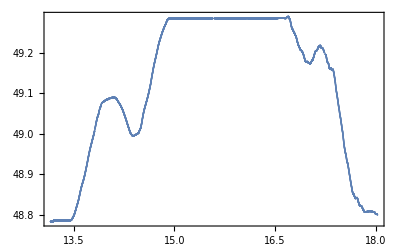

```mathematica
ListPlot[#⟦{4,1}⟧&/@llat,Frame->True,PlotRange->All,Joined->False]
```

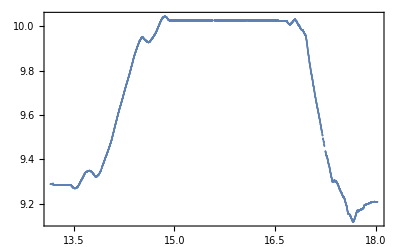

```mathematica
ListPlot[#⟦{4,2}⟧&/@llat,Frame->True,PlotRange->All,Joined->False]
```

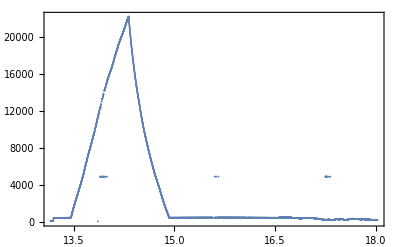

```mathematica
ListPlot[#⟦{4,3}⟧&/@llat,Frame->True,PlotRange->All,Joined->False]
```

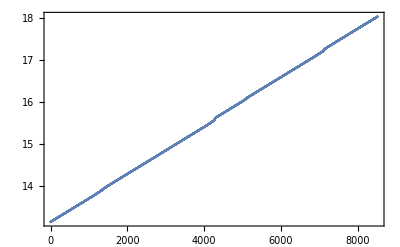

```mathematica
ListPlot[#⟦4⟧&/@llat,Frame->True]
```